```mathematica
α = 2.321995;
β = 0.7256236;
ndist=5;
ndraw=5;
```

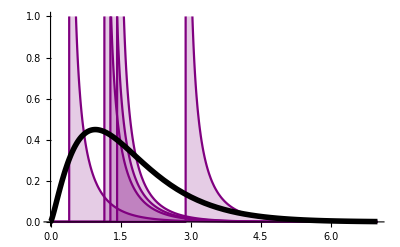

```mathematica
SeedRandom[2];
ψ = 0.1;
li = Sort[RandomVariate[GammaDistribution[(1-ψ)α,β],ndist]];
Show[
Plot[Table[PDF[GammaDistribution[ψ α,β],x-l],{l,li}],{x,0,7},PlotRange->{0,1},PlotStyle->Purple,Filling->Axis],
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All, PlotStyle->{Black, Thickness[0.01]}]]
```

```mathematica
x = Table[li⟦i⟧ + RandomVariate[GammaDistribution[ψ α, β],ndraw],{i,Length[li]}];
y = Table[ConstantArray[i,ndraw],{i,ndist}] ;
```

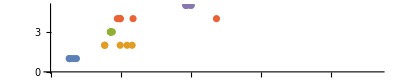

```mathematica
ListPlot[Table[{x⟦i⟧,y⟦i⟧}ᵀ,{i,ndist}], PlotRange->{{0,7},All} ,AspectRatio->.2]
```

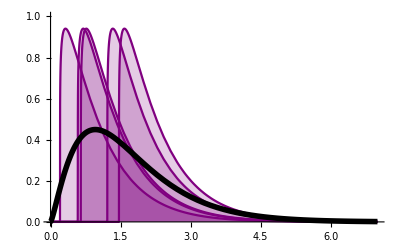

```mathematica
SeedRandom[2];
ψ = 0.5;
li = RandomVariate[GammaDistribution[(1-ψ)α,β],5];
Show[
Plot[Table[PDF[GammaDistribution[ψ α,β],x-l],{l,li}],{x,0,7},PlotRange->{0,1},PlotStyle->Purple,Filling->Axis],
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All, PlotStyle->{Black, Thickness[0.01]}]]
```

```mathematica
x = Table[li⟦i⟧ + RandomVariate[GammaDistribution[ψ α, β],ndraw],{i,Length[li]}];
y = Table[ConstantArray[i,ndraw],{i,ndist}] ;
```

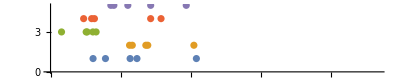

```mathematica
ListPlot[Table[{x⟦i⟧,y⟦i⟧}ᵀ,{i,ndist}], PlotRange->{{0,7},All} ,AspectRatio->.2]
```

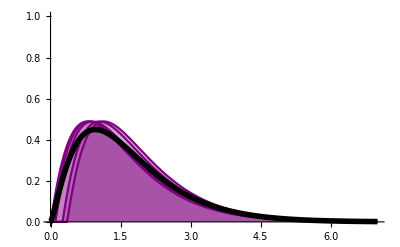

```mathematica
SeedRandom[2];
ψ = 0.9;
li = RandomVariate[GammaDistribution[(1-ψ)α,β],5];
Show[
Plot[Table[PDF[GammaDistribution[ψ α,β],x-l],{l,li}],{x,0,7},PlotRange->{0,1},PlotStyle->Purple,Filling->Axis],
Plot[PDF[GammaDistribution[α,β],x],{x,0,7}, PlotRange->All, PlotStyle->{Black, Thickness[0.01]}]]
```

```mathematica
x = Table[li⟦i⟧ + RandomVariate[GammaDistribution[ψ α, β],ndraw],{i,Length[li]}];
y = Table[ConstantArray[i,ndraw],{i,ndist}] ;
```

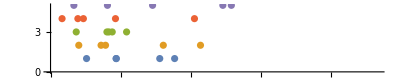

```mathematica
ListPlot[Table[{x⟦i⟧,y⟦i⟧}ᵀ,{i,ndist}], PlotRange->{{0,7},All} ,AspectRatio->.2]
```

```mathematica
influenzaalpha = 2.321995;
influenzabeta = 0.7256236;
influenzaR0=2;
omicronalpha = 2.39;
omicronbeta = 0.3389831;
omicronR0=6;
measlesalpha = 11.35802;
measlesbeta = 0.930985;
measlesR0=12;
```

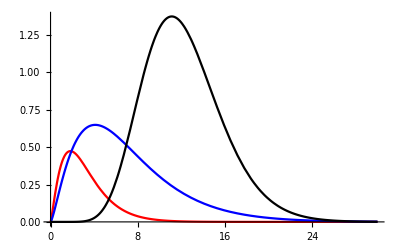

```mathematica
Plot[{
influenzaR0*PDF[GammaDistribution[influenzaalpha, 1/influenzabeta],x],
omicronR0*PDF[GammaDistribution[omicronalpha, 1/omicronbeta],x],
measlesR0*PDF[GammaDistribution[measlesalpha, 1/measlesbeta],x]
},
{x,0,30}, PlotStyle->{Red, Blue, Black}]
```